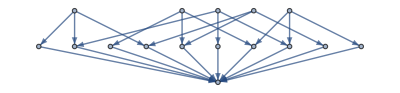

```mathematica
With[{allGraphs=allGraphs5},
Graph[DeleteDuplicates[Join[MobiusGraph4[alfa1Key,allGraphs]//EdgeList,MobiusGraph4[beta1Key,allGraphs]//EdgeList,MobiusGraph4[gamma1Key,allGraphs]//EdgeList,MobiusGraph4[delta1Key,allGraphs]//EdgeList,MobiusGraph4[epsilon1Key,allGraphs]//EdgeList]]]
]
```

```mathematica
MobiusGraphXYZ[key_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=
allGraphs[alfa1Key,"colofourrealnull"]+
allGraphs[beta1Key,"colofourrealnull"]+
allGraphs[gamma1Key,"colofourrealnull"]+
allGraphs[delta1Key,"colofourrealnull"]+
allGraphs[epsilon1Key,"colofourrealnull"],
form3=Map[ChangeSymbol[#]&,
allGraphs[alfa1Key,"colofour"]+
allGraphs[beta1Key,"colofour"]+
allGraphs[gamma1Key,"colofour"]+
allGraphs[delta1Key,"colofour"]+
allGraphs[epsilon1Key,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,edgesTrans,  sublattice},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=Graph[DeleteDuplicates[Join[
MobiusGraph4[alfa1Key,allGraphs]//EdgeList,
MobiusGraph4[beta1Key,allGraphs]//EdgeList,
MobiusGraph4[gamma1Key,allGraphs]//EdgeList,
MobiusGraph4[delta1Key,allGraphs]//EdgeList,
MobiusGraph4[epsilon1Key,allGraphs]//EdgeList]]];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=Descendents[Graph[vars,edges],nonRoot];
sublattice=mob;
Graph[vars,edges,VertexLabels->Table[n->Placed[Tooltip[
TableForm[
With [{baseList=
{
Style[n,12,"Calibri",If[Coefficient[form3,n]==0,Black,Blue]],
Style[Coefficient[form2,n],Bold,If[Coefficient[form2,n]==0,Blue,Red]]
}},
baseList
],TableAlignments->Center],
TableForm[
{found[n,"graph"]}]],{Left}
],{n,vars}],GraphLayout->"LayeredDigraphEmbedding",

GraphHighlight->Join[VertexList[mob],EdgeList[mob]],
GraphHighlightStyle->"Thick",
ImageSize->720]
]
```

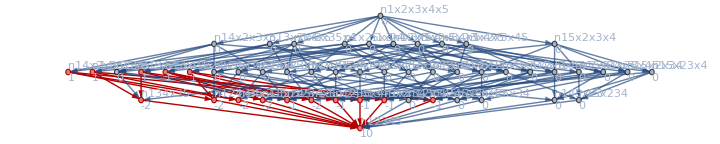

```mathematica
MobiusGraphXYZ[k5Key,allGraphs5]
```

```mathematica
MobiusGraphXYZ2[key_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=
allGraphs[quad1Key,"colofourrealnull"]+
allGraphs[quad2Key,"colofourrealnull"]+
allGraphs[quad3Key,"colofourrealnull"]+
allGraphs[quad4Key,"colofourrealnull"]+
allGraphs[quad5Key,"colofourrealnull"],
form3=Map[ChangeSymbol[#]&,
allGraphs[quad1Key,"colofour"]+
allGraphs[quad2Key,"colofour"]+
allGraphs[quad3Key,"colofour"]+
allGraphs[quad4Key,"colofour"]+
allGraphs[quad5Key,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,edgesTrans,  sublattice},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=Graph[DeleteDuplicates[Join[
MobiusGraph4[quad1Key,allGraphs]//EdgeList,
MobiusGraph4[quad2Key,allGraphs]//EdgeList,
MobiusGraph4[quad3Key,allGraphs]//EdgeList,
MobiusGraph4[quad4Key,allGraphs]//EdgeList,
MobiusGraph4[quad5Key,allGraphs]//EdgeList]]];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=Descendents[Graph[vars,edges],nonRoot];
sublattice=mob;
Graph[vars,edges,VertexLabels->Table[n->Placed[Tooltip[
TableForm[
With [{baseList=
{
Style[n,12,"Calibri",If[Coefficient[form3,n]==0,Black,Blue]],
Style[Coefficient[form2,n],Bold,If[Coefficient[form2,n]==0,Blue,Red]]
}},
baseList
],TableAlignments->Center],
TableForm[
{found[n,"graph"]}]],{Left}
],{n,vars}],GraphLayout->"LayeredDigraphEmbedding",

GraphHighlight->Join[VertexList[mob],EdgeList[mob]],
GraphHighlightStyle->"Thick",
ImageSize->720]
]
```

```mathematica
MobiusGraphBare[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];

(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->TableForm[{n,Style[Coefficient[form,n],Bold,Blue]},TableAlignments->Center],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

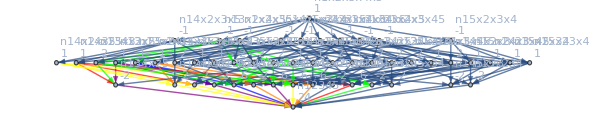

```mathematica
Graph[MobiusGraphBare[K5Key,allGraphs5],
EdgeStyle->Join[
Map[#-> {Thick,Green}&, EdgeList[MobiusGraphBare[quad1Key,allGraphs5]]],
Map[#-> {Thick,Blue}&, EdgeList[MobiusGraphBare[alfa1Key,allGraphs5]]],
Map[#-> {Thick,Red}&, EdgeList[MobiusGraphBare[beta1Key,allGraphs5]]],
Map[#-> {Thick,Orange}&, EdgeList[MobiusGraphBare[gamma1Key,allGraphs5]]],
Map[#-> {Thick,Purple}&, EdgeList[MobiusGraphBare[delta1Key,allGraphs5]]],
Map[#-> {Thick,Yellow}&, EdgeList[MobiusGraphBare[epsilon1Key,allGraphs5]]]
]
]
```

```mathematica
With[g=
```

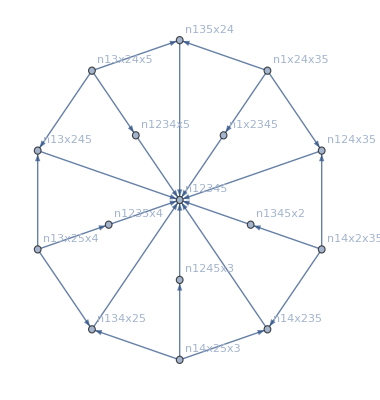

```mathematica
Graph[DeleteDuplicates[
Join[
EdgeList[MobiusGraphBare[alfa1Key,allGraphs5]],
EdgeList[MobiusGraphBare[beta1Key,allGraphs5]],
EdgeList[MobiusGraphBare[gamma1Key,allGraphs5]],
EdgeList[MobiusGraphBare[delta1Key,allGraphs5]],
EdgeList[MobiusGraphBare[epsilon1Key,allGraphs5]]
]
],
GraphLayout->"TutteEmbedding",
VertexLabels->"Name"
]
```

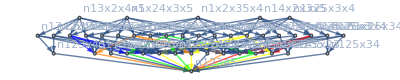

```mathematica
Graph[DeleteDuplicates[
Join[
EdgeList[MobiusGraphBare[quad1Key,allGraphs5]],
EdgeList[MobiusGraphBare[quad2Key,allGraphs5]],
EdgeList[MobiusGraphBare[quad3Key,allGraphs5]],
EdgeList[MobiusGraphBare[quad4Key,allGraphs5]],
EdgeList[MobiusGraphBare[quad5Key,allGraphs5]]
]
],
VertexLabels->"Name",
EdgeStyle->Join[
Map[#-> {Thick,Blue}&, EdgeList[MobiusGraphBare[alfa1Key,allGraphs5]]],
Map[#-> {Thick,Red}&, EdgeList[MobiusGraphBare[beta1Key,allGraphs5]]],
Map[#-> {Thick,Orange}&, EdgeList[MobiusGraphBare[gamma1Key,allGraphs5]]],
Map[#-> {Thick,Green}&, EdgeList[MobiusGraphBare[delta1Key,allGraphs5]]],
Map[#-> {Thick,Yellow}&, EdgeList[MobiusGraphBare[epsilon1Key,allGraphs5]]]
]
]
```